# Cuaderno de prácticas de Álgebra

## Práctica 1

Nombre:
Apellidos:
DNI:
Fecha de nacimiento:
Grupo de teoría:
Grupo de prácticas:

## Ejercicio 1.

Para los grafos del ejercicio 6.8 del manual:

#### Grafo a)

```mathematica
W1 = {1, 2, 3, 4, 5, 6};
F1 = {1 -> 2, 3 -> 1, 4 -> 5, 6 -> 1};

MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];

matriz1 = MATRIZADYACENCIA[W1, F1];
```

#### Grafo b)

```mathematica
matriz2 = {{0, 1, 0,1}, {1,0,1,0},{0,1,0,1},{1,0,1,0}};
```

#### Grafo c)

```mathematica
matrizincidencia={{1, 1,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,1,0,1,0},{0,1,0,1,0,1}};
W=Table[i,{i,Dimensions[matrizincidencia][[1]]}]
F={};
Do[
    AppendTo[F,Position[Transpose[matrizincidencia][[i]],1][[1]][[1]]->Position[Transpose[matrizincidencia][[i]],1][[2]][[1]]]
    ,{i,Dimensions[matrizincidencia][[2]]}];
F
```

```mathematica
W3 = {1,2,3,4,5};
```

```mathematica
F3 = {1->4,1->5,2->4,2->5,3->4,3->5};
```

```mathematica
matriz3 = MATRIZADYACENCIA[W3, F3];
```

#### Grafo d.1)

#### Grafo d.2)

### I) Calcular el número cromático y una coloración óptima

DUDA SOBRE NCOLORACIONES

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

#### Grafo a)

```mathematica
NUMEROCROMATICO[matriz1]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

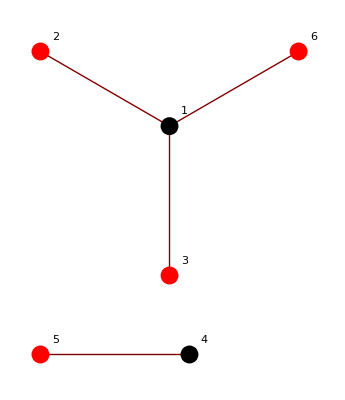

```mathematica
DIBUJAR[matriz1]
```

#### Grafo b)

```mathematica
NUMEROCROMATICO[matriz2]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

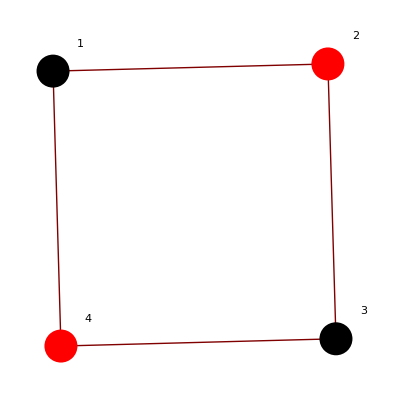

```mathematica
DIBUJAR[matriz2]
```

#### Grafo c)

```mathematica
NUMEROCROMATICO[matriz3]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

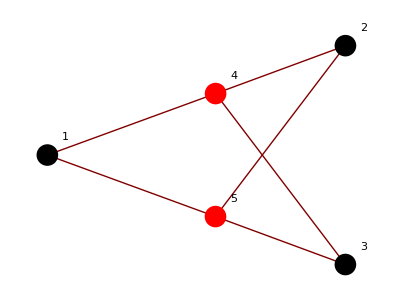

```mathematica
DIBUJAR[matriz3]
```

#### Grafo d.1)

#### Grafo d.2)

### II) Determinar si es plano

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

#### Grafo a)

```mathematica
PLANO[matriz1]
```

True

#### Grafo b)

```mathematica
PLANO[matriz2]
```

True

#### Grafo c)

```mathematica
PLANO[matriz3]
```

True

#### Grafo d.1)

#### Grafo d.2)

### III) Comprobar si es un árbol

```mathematica
CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]

ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

#### Grafo a)

```mathematica
ARBOL[matriz1]
```

False

#### Grafo b)

```mathematica
ARBOL[matriz2]
```

False

#### Grafo c)

```mathematica
ARBOL[matriz3]
```

False

#### Grafo d.1)

#### Grafo d.2)

## Ejercicio 2.

Análogamente para:

### a) Grafo no orientado del ejercicio 5.29

#### i) Calcular el número cromático y una coloración óptima

#### ii) Determinar si es plano

#### iii) Comprobar si es un árbol

### b) Un octógono

#### i) Calcular el número cromático y una coloración óptima

#### ii) Determinar si es plano

#### iii) Comprobar si es un árbol

### c) K8

#### i) Calcular el número cromático y una coloración óptima

#### ii) Determinar si es plano

#### iii) Comprobar si es un árbol

### d) K2, 3

#### i) Calcular el número cromático y una coloración óptima

#### ii) Determinar si es plano

#### iii) Comprobar si es un árbol